# Thermo field double of dS black hole

7/26/2021
Ref: Mathematical Physics on a Quantum Computer by Yuan Feng and Michael McGuigan
https://arxiv.org/pdf/1911.03335.pdf
https://lib-extopc.kek.jp/preprints/PDF/1988/8811/8811283.pdf

#### Eqn’s from ref [3]:

|n_B,n_F;ñ_B,ñ_F⟩=|n_B,n_F⟩⊗|ñ_B,ñ_F⟩

G=-ⅈθ[β](ã_F a_F-a_F^+ã_F^+)-ⅈθ^-[β](ã_B a_B-a_B^+ã_B^+)
tanθ[β]=e^(-βm/2)=tanh θ^-[β]
β=1/kT
where I think k is the Stefan Boltzmann constant

Note that in the above eqn for G, we only need a_B because we only need double bosons, no fermions.
G=-ⅈθ[β](ã_B a_B-a_B^+ã_B^+)

#### Plot of theta as a function of β,

```mathematica
θ[β_]:=ArcTanh[Exp[-β/2]]
```

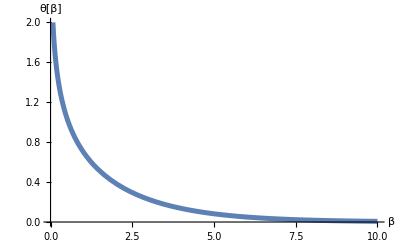

```mathematica
Plot[θ[β],{β,0,10},PlotRange->{0,2},AxesLabel->{"β","θ[β]"},BaseStyle->{FontWeight->"Bold",FontSize->12},PlotStyle->{Thickness[0.009]}]
```

#### We want to define the boson and his double. Use KroneckerProduct to get the boson’s raising operator, aB, and the thermo double’s raising operator, aBd,

```mathematica
aB:=KroneckerProduct[({{0, √1, 0, 0, 0, 0, 0, 0}, {0, 0, √2, 0, 0, 0, 0, 0}, {0, 0, 0, √3, 0, 0, 0, 0}, {0, 0, 0, 0, √4, 0, 0, 0}, {0, 0, 0, 0, 0, √5, 0, 0}, {0, 0, 0, 0, 0, 0, √6, 0}, {0, 0, 0, 0, 0, 0, 0, √7}, {0, 0, 0, 0, 0, 0, 0, 0}}),IdentityMatrix[8]]
aBd:=KroneckerProduct[IdentityMatrix[8],({{0, √1, 0, 0, 0, 0, 0, 0}, {0, 0, √2, 0, 0, 0, 0, 0}, {0, 0, 0, √3, 0, 0, 0, 0}, {0, 0, 0, 0, √4, 0, 0, 0}, {0, 0, 0, 0, 0, √5, 0, 0}, {0, 0, 0, 0, 0, 0, √6, 0}, {0, 0, 0, 0, 0, 0, 0, √7}, {0, 0, 0, 0, 0, 0, 0, 0}})]
G:=-ⅈ(aBd.aB-ConjugateTranspose[aB].ConjugateTranspose[aBd])
```

```mathematica
Print[G]
```

{{0,0,0,0,0,0,0,0,0,-ⅈ,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,-ⅈ √2,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,-ⅈ √3,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,-2 ⅈ,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,-ⅈ √5,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,-ⅈ √6,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,-ⅈ √7,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,-ⅈ √2,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{ⅈ,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,-2 ⅈ,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,ⅈ √2,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,-ⅈ √6,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,ⅈ √3,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,-2 ⅈ √2,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,2 ⅈ,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,-ⅈ √10,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,ⅈ √5,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,-2 ⅈ √3,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,ⅈ √6,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,-ⅈ √14,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,ⅈ √7,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,-ⅈ √3,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,ⅈ √2,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,-ⅈ √6,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,2 ⅈ,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,-3 ⅈ,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,ⅈ √6,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,-2 ⅈ √3,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,2 ⅈ √2,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,-ⅈ √15,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,ⅈ √10,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,-3 ⅈ √2,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,2 ⅈ √3,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,-ⅈ √21,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,ⅈ √14,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,-2 ⅈ,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,ⅈ √3,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,-2 ⅈ √2,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,ⅈ √6,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,-2 ⅈ √3,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,3 ⅈ,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,-4 ⅈ,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,2 ⅈ √3,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,-2 ⅈ √5,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,ⅈ √15,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,-2 ⅈ √6,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,3 ⅈ √2,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,-2 ⅈ √7,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,ⅈ √21,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,-ⅈ √5,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,2 ⅈ,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,-ⅈ √10,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,2 ⅈ √2,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,-ⅈ √15,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,2 ⅈ √3,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,-2 ⅈ √5,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,4 ⅈ,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,-5 ⅈ,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,2 ⅈ √5,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,-ⅈ √30,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,2 ⅈ √6,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,-ⅈ √35,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,2 ⅈ √7,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,-ⅈ √6,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,ⅈ √5,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,-2 ⅈ √3,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,ⅈ √10,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,-3 ⅈ √2,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,ⅈ √15,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,-2 ⅈ √6,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,2 ⅈ √5,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,-ⅈ √30,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,5 ⅈ,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,-6 ⅈ,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,ⅈ √30,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,-ⅈ √42,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,ⅈ √35,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,-ⅈ √7,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,ⅈ √6,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,-ⅈ √14,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,2 ⅈ √3,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,-ⅈ √21,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,3 ⅈ √2,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,-2 ⅈ √7,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,2 ⅈ √6,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,-ⅈ √35,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,ⅈ √30,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,-ⅈ √42,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,6 ⅈ,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,-7 ⅈ},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,ⅈ √42,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,ⅈ √7,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,ⅈ √14,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,ⅈ √21,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,2 ⅈ √7,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,ⅈ √35,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,ⅈ √42,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,7 ⅈ,0,0,0,0,0,0,0,0,0}}

```mathematica
Print[Chop[G]]
```

{{0,0,0,0,0,0,0,0,0,-ⅈ,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,-ⅈ √2,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,-ⅈ √3,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,-2 ⅈ,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,-ⅈ √5,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,-ⅈ √6,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,-ⅈ √7,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,-ⅈ √2,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{ⅈ,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,-2 ⅈ,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,ⅈ √2,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,-ⅈ √6,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,ⅈ √3,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,-2 ⅈ √2,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,2 ⅈ,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,-ⅈ √10,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,ⅈ √5,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,-2 ⅈ √3,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,ⅈ √6,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,-ⅈ √14,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,ⅈ √7,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,-ⅈ √3,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,ⅈ √2,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,-ⅈ √6,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,2 ⅈ,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,-3 ⅈ,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,ⅈ √6,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,-2 ⅈ √3,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,2 ⅈ √2,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,-ⅈ √15,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,ⅈ √10,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,-3 ⅈ √2,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,2 ⅈ √3,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,-ⅈ √21,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,ⅈ √14,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,-2 ⅈ,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,ⅈ √3,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,-2 ⅈ √2,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,ⅈ √6,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,-2 ⅈ √3,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,3 ⅈ,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,-4 ⅈ,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,2 ⅈ √3,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,-2 ⅈ √5,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,ⅈ √15,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,-2 ⅈ √6,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,3 ⅈ √2,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,-2 ⅈ √7,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,ⅈ √21,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,-ⅈ √5,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,2 ⅈ,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,-ⅈ √10,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,2 ⅈ √2,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,-ⅈ √15,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,2 ⅈ √3,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,-2 ⅈ √5,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,4 ⅈ,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,-5 ⅈ,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,2 ⅈ √5,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,-ⅈ √30,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,2 ⅈ √6,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,-ⅈ √35,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,2 ⅈ √7,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,-ⅈ √6,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,ⅈ √5,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,-2 ⅈ √3,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,ⅈ √10,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,-3 ⅈ √2,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,ⅈ √15,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,-2 ⅈ √6,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,2 ⅈ √5,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,-ⅈ √30,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,5 ⅈ,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,-6 ⅈ,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,ⅈ √30,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,-ⅈ √42,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,ⅈ √35,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,-ⅈ √7,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,ⅈ √6,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,-ⅈ √14,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,2 ⅈ √3,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,-ⅈ √21,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,3 ⅈ √2,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,-2 ⅈ √7,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,2 ⅈ √6,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,-ⅈ √35,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,ⅈ √30,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,-ⅈ √42,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,6 ⅈ,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,-7 ⅈ},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,ⅈ √42,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,ⅈ √7,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,ⅈ √14,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,ⅈ √21,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,2 ⅈ √7,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,ⅈ √35,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,ⅈ √42,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,7 ⅈ,0,0,0,0,0,0,0,0,0}}

```mathematica
SetDirectory[NotebookDirectory[]];
saveHam[ham_] :=Export["./"<>"GdsBH8x8.txt", ham, "Table"]

saveHam[N[G]];
```

```mathematica
θ[β_]:=ArcTanh[Exp[-β/2]]
```

#### Apply eqn e^-ⅈθG to evolve G in theta (inverse temp),

```mathematica
h1[β_]:=N[MatrixExp[-ⅈ*θ[β]G][[1,1]]]
h2[β_]:=N[MatrixExp[-ⅈ*θ[β]G][[10,1]]]
h3[β_]:=N[MatrixExp[-ⅈ*θ[β]G][[19,1]]]
h4[β_]:=N[MatrixExp[-ⅈ*θ[β]G][[28,1]]]
h5[β_]:=N[MatrixExp[-ⅈ*θ[β]G][[37,1]]]
h6[β_]:=N[MatrixExp[-ⅈ*θ[β]G][[46,1]]]
h7[β_]:=N[MatrixExp[-ⅈ*θ[β]G][[55,1]]]
h8[β_]:=N[MatrixExp[-ⅈ*θ[β]G][[64,1]]]
```

This is as close as we can get with 8x8, we’d need infinity to get exact result.

#### Plot of the Boltzmann probabilities as a function of β,

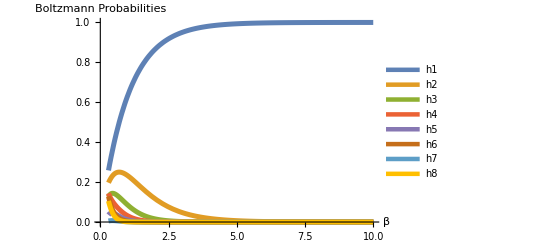

```mathematica
Plot[{(Abs[h1[β]])^2,(Abs[h2[β]])^2,(Abs[h3[β]])^2,  (Abs[h4[β]])^2,(Abs[h5[β]])^2,(Abs[h6[β]])^2,(Abs[h7[β]])^2,(Abs[h8[β]])^2}, {β,.3,10},PlotRange->{0,1},BaseStyle->{FontWeight->"Bold",FontSize->12},AxesLabel->{"β","Boltzmann Probabilities"},PlotStyle->{Thickness[0.009]},PlotLegends->{"h1","h2","h3","h4","h5","h6","h7","h8"}]
```

#### Woop Woop! The plot below is what we were aiming for,

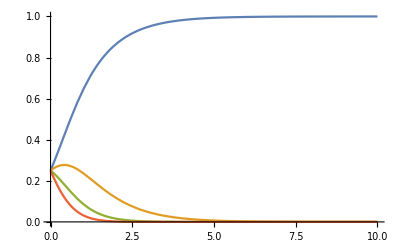

```mathematica
Plot[{ⅇ^(-β 0)/(ⅇ^(-β 0)+ⅇ^(-β 1)+ⅇ^(-β 2)+ⅇ^(-β 3)),ⅇ^(-β 1)/(ⅇ^(-β 0)+ⅇ^(-β 1)+ⅇ^(-β 2)+ⅇ^(-β 3)),ⅇ^(-β 2)/(ⅇ^(-β 0)+ⅇ^(-β 1)+ⅇ^(-β 2)+ⅇ^(-β 3)),ⅇ^(-β 3)/(ⅇ^(-β 0)+ⅇ^(-β 1)+ⅇ^(-β 2)+ⅇ^(-β 3))},{β,0,10}]
```